```mathematica
ClearAll[Evaluate[Context[]<>"*"]]
```

```mathematica
Needs["Spline`"]
```

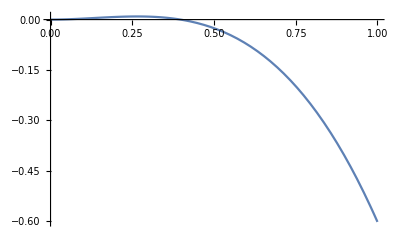

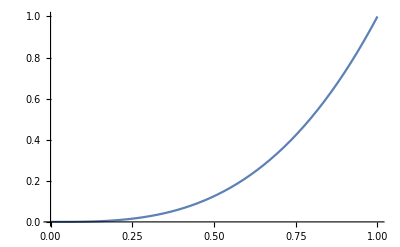

t^3

-t (t^2+2 t Cot[π/8]-2 t Csc[π/8])

```mathematica
P2={{1,t,t^2}};
Coef2 = {{1,0,0},{-1,1,0},{0,-1,1}};
H2=H2[Coef2,IdentityMatrix[3],{0,0},{1/2,1/2 (1-Cos[π/8]) Csc[π/8]},{1,0}];
cp2=CharacteristicPolynomial[Coef2.H2,t];
Plot[cp2,{t,0,1}]
Plot[BS[3,3,t],{t,0,1}]
BS[3,3,t]
cp2
```

```mathematica
Clear[t];MatrixForm[Coef2.H2]
evals=Eigenvalues[Coef2.H2]
Det[Coef2.H2-evals[[1]]*IdentityMatrix[3]]
Det[Coef2.H2-t*IdentityMatrix[3]]
charpol=CharacteristicPolynomial[Coef2.H2,t]
```

(0 | 0 | 0
1 | -2 (-1+Cos[π/8]) Csc[π/8] | 0
0 | 2 (-1+Cos[π/8]) Csc[π/8] | 0)

{-2 (-1+Cos[π/8]) Csc[π/8],0,0}

0

-t (t^2+2 t Cot[π/8]-2 t Csc[π/8])

-t (t^2+2 t Cot[π/8]-2 t Csc[π/8])

```mathematica
N[evals[[1]]]
```

0.397825

```mathematica
roots = Solve[charpol==0,{t}]
N[roots[[3]][[1]]][[2]]
```

{{t→0},{t→0},{t→2 (-Cot[π/8]+Csc[π/8])}}

0.397825

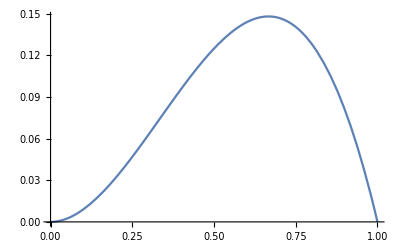

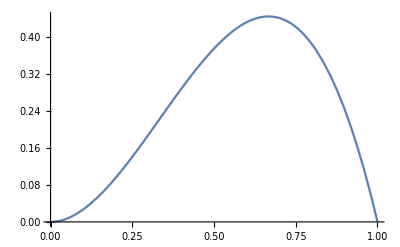

3/8

1/8

```mathematica
P2={{1,t,t^2}};
Coef2 = {{1,0,0},{-1,1,0},{0,-1,1}};
H2={{0,0,0},{1,1,0},{1,0,0}};
cp2=CharacteristicPolynomial[Coef2.H2,t];
Plot[cp2,{t,0,1}]
Plot[BS[3,2,t],{t,0,1}]
t=1/2;
BS[3,2,t]
cp2
```

```mathematica
MatrixForm[Coef2.H2]
Eigenvectors[Coef2.H2]
Coef2.H2.Eigenvectors[Coef2.H2][[1]]
Coef2.H2.Eigenvectors[Coef2.H2][[2]]
Coef2.H2.Eigenvectors[Coef2.H2][[3]]
```

(0 | 0 | 0
1 | 1 | 0
0 | -1 | 0)

{{0,-1,1},{0,0,1},{0,0,0}}

{0,-1,1}

{0,0,0}

{0,0,0}

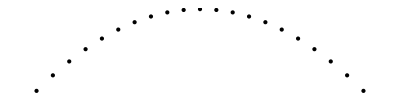

```mathematica
points2 = Table[v=P2.Coef2.H2;{v[[1]][[1]],v[[1]][[2]]},{t,0,1,1/20}];
Graphics[Point[points2],PlotRange->All]
```

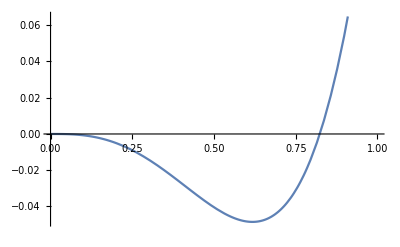

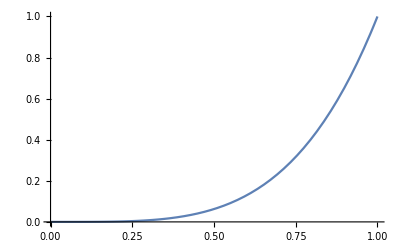

t^4

4 (1-t) t^3

24 (1-t)^2 t^2

144 (1-t)^3 t

576 (1-t)^4

-1/256 t (-288 t^2+288 √3 t^2-256 t^3)

```mathematica
Clear[t];
P3={{1,t,t^2,t^3}};
Coef3 = {{1,0,0,0},{-1,1,0,0},{0,-1,1,0},{0,0,-1,1}};
H3=H3[ Coef3,IdentityMatrix[4],{0,0},{1/2+1/4 (1-√3),(-1/(√2)+(1+√3)/(2 √2))/(√2)},{1/2+1/4 (-1+√3),(-1/(√2)+(1+√3)/(2 √2))/(√2)},{1,0}];
cp3=CharacteristicPolynomial[Coef3.H3,t];
Plot[cp3,{t,0,1}]
Plot[BS[4,4,t],{t,0,1}]
BS[4,4,t]
BS[4,3,t]
BS[4,2,t]
BS[4,1,t]
BS[4,0,t]
cp3
```

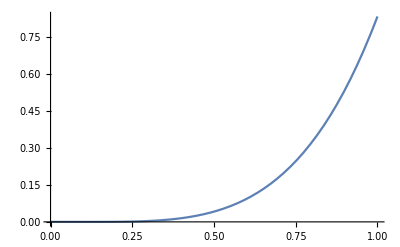

-Graphics-

1/16

1/24

```mathematica
Clear[t];
P3={{1,t,t^2,t^3}};
Coef3 = {{1,0,0,0},{-1,1,0,0},{0,-1,1,0},{0,0,-1,1}};
H3={{0,0,0,0},{1/3,1/6,0,0},{2/3,1/6,0,0},{1,0,0,0}};
cp3=CharacteristicPolynomial[Coef3.H3,t];
Plot[cp3,{t,0,1}]
Plot[BS[4,4,t],{t,0,1}]
t=1/2;
BS[4,4,t]
cp3
```

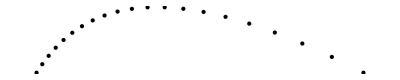

```mathematica
points3 = Table[v=P3.Coef3.H3;{v[[1]][[1]],v[[1]][[2]]},{t,0,1,1/20}];
Graphics[Point[points3],PlotRange->All]
```